```mathematica
AoA=Table[n,{n,-0.3,0.3,0.1}];
```

```mathematica
DecimalForm[AoA,{1,2}]
```

{-0.30,-0.20,-0.10,0.00,0.10,0.20,0.30}

```mathematica
points=ToExpression[Import["/home/tatjam/code/tfg/workdir/geom.dat","String"]];
```

```mathematica
Graphics3D[Polygon[points]]
```

-Graphics3D-

```mathematica
params=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/params_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"]&,AoA];
```

```mathematica
liftOverCamber=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"][[1]]&,AoA];
```

```mathematica
clOverCamberPrandtl=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"][[1]]&,AoA];
```

```mathematica
sln=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/sln_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"][[1]]&,AoA];
```

```mathematica
wakeGeom=Map[ToExpression[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/wake_geom_" <> ToString[DecimalForm[#, {1, 2}]] <> "_.dat","String"]]&, AoA];
```

```mathematica
wakesln=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/wake_sln_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"][[1]]&,AoA];
```

```mathematica
maxsol=Map[Max[Abs[#]]&, sln];
```

```mathematica
maxsolwake=Map[Max[Abs[#]]&, wakesln];
```

```mathematica
colorEach[p_,c_,i_]:={FaceForm[ColorData["GrayYellowTones"][Abs[c/maxsol[[i]]]]],Polygon[p]}
```

```mathematica
colorEachWrapper[i_][p_,c_]:=colorEach[p,c,i]
```

```mathematica
colorEachWake[p_,c_,i_]:={FaceForm[ColorData["TemperatureMap"][Abs[c/maxsolwake[[i]]]]],Polygon[p]}
```

```mathematica
colorEachWrapperWake[i_][p_,c_]:=colorEachWake[p,c,i]
```

#### Lifting line theory

#### Comparison

```mathematica
graphics0=Map[Legended[Graphics3D[
ArrayFlatten[{EdgeForm[None],MapThread[colorEachWrapper[#],{points, sln[[#]]}],
MapThread[colorEachWrapperWake[#], {wakeGeom[[#]], wakesln[[#]]}]},1],Lighting->{{"Ambient", White}}],{BarLegend[{"GrayYellowTones",{0,maxsol[[#]]}}],
BarLegend[{"TemperatureMap", {0,maxsolwake[[#]]}}]}]&,Table[n,{n,1,Length[AoA]}]];
```

```mathematica
graphics=Map[ListLinePlot[{liftOverCamber[[#]]*(1+1/(2π)),clOverCamberPrandtl[[#]]},
Epilog->{InfiniteLine[{0,AoA[[#]]*2π},{1,0}]},PlotLabel->AoA[[#]],PlotLegends->{"Panels", "Prandtl"}]&,Table[n,{n,1,Length[AoA]}]];
```

```mathematica
graphics0[[5]]
```

-Graphics3D-

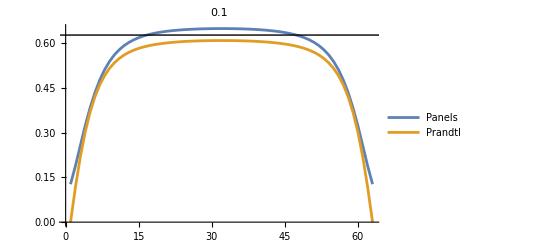

```mathematica
graphics[[5]]
```

```mathematica
mat=Import["/home/tatjam/code/tfg/workdir/steady_rectangle/dyn_mat_0.20_.dat"];
```

```mathematica
Mean[Mean[mat]]
```

0.0120284

```mathematica
Max[mat]
```

10.0077

```mathematica
Min[mat]
```

0